```mathematica
(* Lennard Jones potential *)
```

General::ivar: 0.0724207 is not a valid variable.

General::ivar: 0.0931064 is not a valid variable.

General::ivar: 0.113792 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

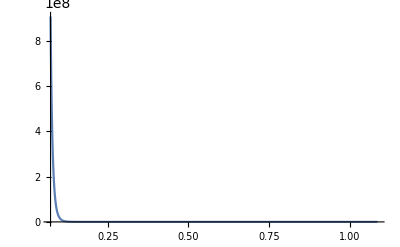

```mathematica
U[r_]:=4 ϵ ((σ/r)^12-(σ/r)^6);
f[r_]:=-D[U[r],r];
ϵ=0.929;(* Argon *)
σ=0.362;
Plot[{U[r],f[r]},{r,0.2σ,3 σ},PlotRange->All]
```

```mathematica
(* := means "using when you need it",so when U(r) appears in "Plot", numbers have been plugged in, it's been converted into a bunch of numbers, and we can't ask for f[r] then. *)
(* solution no.1 *)
```

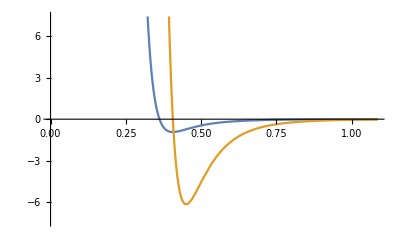

```mathematica
U[r_]:=4 ϵ ((σ/r)^12-(σ/r)^6);
f[r_]=-D[U[r],r];
ϵ=0.929;(* Argon *)
σ=0.362;
Plot[{U[r],f[r]},{r,0.1σ,3 σ},PlotRange->{-8 ϵ,8 ϵ}]
```

```mathematica
(* solution no.2 *)
```

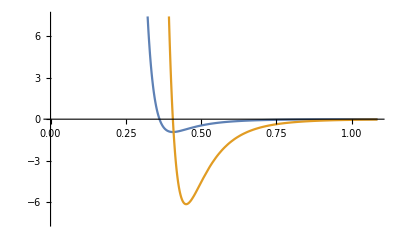

```mathematica
U[r_]:=4 ϵ ((σ/r)^12-(σ/r)^6);
f[r_]:=-D[U[r],r];
ϵ=0.929;(* Argon *)
σ=0.362;
Plot[{U[r],f[t]/.t->r},{r,0.2σ,3 σ},PlotRange->{-8 ϵ,8 ϵ}]
```

```mathematica
(* solution no.3 *)
```

```mathematica
U[r_]:=4 ϵ ((σ/r)^12-(σ/r)^6);
f[r_]:=Evaluate[-D[U[r],r]];
ϵ=0.929;(* Argon *)
σ=0.362;
Plot[{U[r],f[r]},{r,0.1σ,3 σ},PlotRange->{-8 ϵ,8 ϵ}]
```

-Graphics-